#### Please see bottom of file for testing the new canvases

The goal of this code is to establish a metric function to compare thread density weave maps obtained from painting canvases. Establishing the degree of similarity between two canvases allows us to conclude whether the source of the canvases is the same or not, which has important implications in the study of paintings. The main function of this algorithm is distWeaveMap and its helper functions are documented separately in the first part of the document. The second part of the notebook consists of various performance tests and its results.

```mathematica
allFiles=FileNames["*.m",NotebookDirectory[]<>"weaveMaps/"];
```

This method ensures that the images have horizontal stipes

```mathematica
horizontal::usage="This function takes an image as input and ouputs the image rotated so that its stripes are horizontal. By construction of clean and display functions, it is important to pass any image to be analyzed through the horizontal function first in order to ensure proper functionality"

horizontal[canvas_]:=Module[{lines, verticalCount, current, i, horizontalCount},
 
lines =ImageLines[EdgeDetect[Image[display[canvas,0]],1,0.1],MaxFeatures->100];
verticalCount=0;
horizontalCount = 0;

	For[i=1,i≤Length[lines],i++,
	current=lines[[i,1]];
	
	If[Abs[current[[1,2]]-current[[2,2]]]>1 && Abs[current[[1,1]]-current[[2,1]]] < Dimensions[canvas][[2]]/2,
	verticalCount++;];
	If[Abs[current[[1,1]]-current[[2,1]]]>1 && Abs[current[[1,2]]-current[[2,2]]] < Dimensions[canvas][[1]]/2,
	horizontalCount++;];
];
(*Depending on whether most lines are horizontal or vertical, output original or rotated image*)
If[verticalCount>horizontalCount,
Return[Transpose[canvas]];,
Return[canvas];]
];
```

This function takes an image as input and ouputs the image rotated so that its stripes are horizontal. By construction of clean and display functions, it is important to pass any image to be analyzed through the horizontal function first in order to ensure proper functionality

This is a method to display the canvases clearly for accurate comparison

```mathematica
display::usage="The method takes a canvas matrix as input and outputs an image that has sharper edges by enhancing the weights of the individual columns. We assume the stripes in the images are horizontal"

display[matrix_,param_]:=Module[{output, i},
output = matrix;
For[i=1,i≤Dimensions[output][[1]],i++,
output[[i,All]] = output[[i,All]]+param*Mean[output[[i,All]]];
];

Return[ArrayPlot[output, ColorFunction->"ThermometerColors"]];
];
```

The method takes a canvas matrix as input and outputs an image that has sharper edges by enhancing the weights of the individual columns. We assume the stripes in the images are horizontal

This is an implementation of the pre - processing algorithm to clean up the images

```mathematica
clean::usage="This function reduces the noise of the images by application of CommonestFilter"

clean[canvas_]:=Module[{output, i},
output =canvas;
For[i=1,i≤Dimensions[output][[1]],i++,
output[[i,All]] = output[[i,All]]-2*Mean[output[[i,All]]];
];
output = CommonestFilter[output,{1,3}];
Return[output];
];
```

This function reduces the noise of the images by application of CommonestFilter

This function computes the distance between two rows of different sizes.

```mathematica
rowDistance::usage="This function computes the distance between two given canvases rows. It takes as input the individual rows and outputs their euclidean distance. The function has the option of considering multiple overlaps of the smaller row with respect to the larger one. In this case, the function outputs the minimum distance across all overlaps (see commented code)."

rowDistance[row1_, row2_]:=Module[{col1, col2, smallCol, largeCol, smallLen, largeLen, rangeL, startL},

col1 = Length[row1];
col2 = Length[row2];

If[col1≥ col2,smallCol = row2; largeCol = row1, smallCol = row1; largeCol = row2];

(*This is the code to calculate distance for multiple alignments*)
(*
min = Power[10,10];
numPlaces = Length[largeCol]-Length[smallCol]+ 1;	
jumpSize = 20; 

For[j=1, j<= numPlaces, j=j+jumpSize,

		rowsLargeCol = largeCol[[j;;j+Length[smallCol]-1]];
		d = EuclideanDistance[rowsLargeCol,smallCol];

		If[d<min, min=d; imin = j;];	
];
*)

(*centralize small row in larger one and compute distance*)

smallLen = Length[smallCol];
largeLen = Length[largeCol];

rangeL = Range[startL = Floor[(largeLen-smallLen)/2]+1, startL+smallLen-1];

Return[EuclideanDistance[largeCol[[rangeL]], smallCol]];
];
```

This function computes the distance between two given canvases rows. It takes as input the individual rows and outputs their euclidean distance. The function has the option of considering multiple overlaps of the smaller row with respect to the larger one. In this case, the function outputs the minimum distance across all overlaps (see commented code).

compare function goes below:

```mathematica
compare::usage="This function computes the minimum distance across the relevant overlaps between the input canvases. The inputs are assumeds to have stripes oriented horizontally (ensured by horizontal function). By relevant, we mean overlaps that include at least half of the number of rows in the image with the least rows. The output consists of the minimum distance and the row index i of the image with more rows that corresponds to the best alignment. To visualize the best alignment, we align row i with the center of the image with fewer rows."

compare[img1_, img2_]:=Module[{numRows1,numRows2,middleRowOfIm2,bestDistance,bestDistanceRowOfIm1,i,overallDistance,numRowsCompared,j, im1, im2},

(*Force im1 to be the one with more rows.*)
numRows1 = Dimensions[img1][[1]];
numRows2 = Dimensions[img2][[1]];

If[numRows1 < numRows2,{im1, im2} = {img2, img1}, {im1,im2} = {img1, img2}];

numRows1 = Dimensions[im1][[1]];
numRows2 = Dimensions[im2][[1]];
middleRowOfIm2=Ceiling[numRows2/2];

bestDistance=Power[10,10];
bestDistanceRowOfIm1=-1;

(*Iterate through possible overlaps between canvases*)
For[i=1,i≤numRows1,i++,
overallDistance=0;
numRowsCompared=0;
For[j=1,j≤numRows2,j++,
If[1≤i+j-middleRowOfIm2≤numRows1,
overallDistance+=Power[rowDistance[im1[[i+j-middleRowOfIm2, All]],im2[[j, All]]],2];
numRowsCompared++;
];
];

(*correct distance for number of row used in comparisson*)
overallDistance=Sqrt[overallDistance];
overallDistance/=numRowsCompared;

If[overallDistance<bestDistance,
bestDistance=overallDistance;
bestDistanceRowOfIm1=i;
];
];
Return[{bestDistance,bestDistanceRowOfIm1}];
];
```

This function computes the minimum distance across the relevant overlaps between the input canvases. The inputs are assumeds to have stripes oriented horizontally (ensured by horizontal function). By relevant, we mean overlaps that include at least half of the number of rows in the image with the least rows. The output consists of the minimum distance and the row index i of the image with more rows that corresponds to the best alignment. To visualize the best alignment, we align row i with the center of the image with fewer rows.

This is the main function that calculates the minimum distance between two canvases and the overlap that gives the minimum distance.

```mathematica
distWeaveMapsZJF::usage="This function uses the functions above to compute the minimum distance and the best overlap between the two input canvases. The input is the unclean version of both canvases. The output consists of {dmin,i, longer, shorter}, where dmin and i come from the call to compare function that yields smallest distance and longer and shorter correspond to the input canvases rotated appropriately"

distWeaveMapsZJF[canvas1_, canvas2_]:=Module[{hcanvas1, hcanvas2, clean1, clean2, d1,d2, i1,i2, dmin, longer, shorter},

(*Make sure both images have horizontal stripes*)
hcanvas1 = horizontal[canvas1];
hcanvas2 = horizontal[canvas2];
If[Dimensions[hcanvas1][[1]]>Dimensions[hcanvas2][[1]],longer= hcanvas1;shorter=hcanvas2, longer= hcanvas2;shorter=hcanvas1];

(*Pre-processing: we clean up the images to reduce noise and smooth data*)
clean1 = clean[hcanvas1];
clean2 = clean[hcanvas2];

(*compute the minimum distance across all possible orientations of the images. We fix clean1 and consider all relevant orientations for clean2*)
{d1, i1} = compare[clean1, clean2];
Print["50% complete"];
{d2, i2} = compare[clean1, Reverse[clean2]];
Print["Done!"];

(*Since images are assumed to have horizontal stripes, the rotations below do not contribute much to the accuracy of the algorithm 
bu increase runtime. For some images, it might be useful to uncomment the lines for slighlty better accuracy*)
(*
{d3, i3} = compare[clean1, Reverse[clean2,2]];
{d4, i4} = compare[clean1, Reverse[Reverse[clean2],2]];
*)

dmin = Min[d1,d2];
If[dmin==d1, Return[{dmin,i1, longer, shorter}];];
If[dmin==d2, Return[{dmin,i2, longer, Reverse[shorter]}];];

];
```

This function uses the functions above to compute the minimum distance and the best overlap between the two input canvases. The input is the unclean version of both canvases. The output consists of {dmin,i, longer, shorter}, where dmin and i come from the call to compare function that yields smallest distance and longer and shorter correspond to the input canvases rotated appropriately

Testing section below:

```mathematica
(*
Get[allFiles[[1]]];
t1 = matV;
t2 = matH;
Get[allFiles[[2]]];
t3 = matV;
t4 = matH;

Get[allFiles[[3]]];
t5 = matV;
t6 = matH;
Get[allFiles[[4]]];
t7 = matV;
t8 = matH;
*)

(*The results for these calls to the function are shwon below*)
(*
output1=distWeaveMapsZJF[t2,t4];
output2 = distWeaveMapsZJF[t5,t7];
*)
```

The results for output1 are shown below, where the images have been aligned by using the index in output1 as explained above. In this case, d = 1.38567.

```mathematica
(*ref1 = Line[{{0,Dimensions[output1[[3]]][[1]]-output1[[2]]},{Dimensions[output1[[3]]][[2]],Dimensions[output1[[3]]][[1]]-output1[[2]]}}];
ref2 = Line[{{0,Dimensions[output1[[4]]][[1]]/2},{Dimensions[output1[[4]]][[2]],Dimensions[output1[[4]]][[1]]/2}}];
GraphicsRow[{Show[display[output1[[3]],1],Graphics[{Black,ref1}]],Show[display[output1[[4]],1], Graphics[{Black, ref2}]]}]*)
```

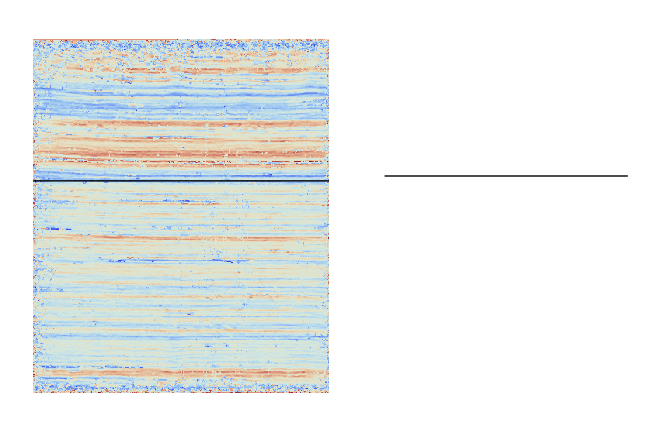

-Graphics-

The results for output2 are shown below, where the images have been aligned by using the index in output1 as explained above. In this case, d = 0.467234

```mathematica
(*ref3= Line[{{0,Dimensions[output2[[3]]][[1]]-output2[[2]]},{Dimensions[output2[[3]]][[2]],Dimensions[output2[[3]]][[1]]-output2[[2]]}}];
ref4 = Line[{{0,Dimensions[output2[[4]]][[1]]/2},{Dimensions[output2[[4]]][[2]],Dimensions[output2[[4]]][[1]]/2}}];
GraphicsRow[{Show[display[output2[[3]],1],Graphics[{Black,ref3}]],Show[display[output2[[4]],1], Graphics[{Black, ref4}]]}]*)
```

-Graphics-

# Testing of other canvases:

```mathematica
distWeaveMapsZJ::usage="This is a repetition of distWeaveMapsZJ above with all the outputs except the distance surpressed for testing"

distWeaveMapsZJ[canvas1_, canvas2_]:=Module[{hcanvas1, hcanvas2, clean1, clean2, d1,d2, i1,i2, dmin, longer, shorter},

(*Make sure both images have horizontal stripes*)
hcanvas1 = horizontal[canvas1];
hcanvas2 = horizontal[canvas2];
If[Dimensions[hcanvas1][[1]]>Dimensions[hcanvas2][[1]],longer= hcanvas1;shorter=hcanvas2, longer= hcanvas2;shorter=hcanvas1];

(*Pre-processing: we clean up the images to reduce noise and smooth data*)
clean1 = clean[hcanvas1];
clean2 = clean[hcanvas2];

(*compute the minimum distance across all possible orientations of the images. We fix clean1 and consider all relevant orientations for clean2*)
{d1, i1} = compare[clean1, clean2];
Print["50% complete"];
{d2, i2} = compare[clean1, Reverse[clean2]];
Print["Done!"];

(*Since images are assumed to have horizontal stripes, the rotations below do not contribute much to the accuracy of the algorithm 
bu increase runtime. For some images, it might be useful to uncomment the lines for slighlty better accuracy*)
(*
{d3, i3} = compare[clean1, Reverse[clean2,2]];
{d4, i4} = compare[clean1, Reverse[Reverse[clean2],2]];
*)

Return[Min[d1,d2]];

];
```

This is a repetition of distWeaveMapsZJ above with all the outputs except the distance surpressed for testing